```mathematica
graph={{0.3461717838632017,1.4984640297338632},{0.6316400411846113,2.5754677320579895},{1.3906262250927481,2.164978861396621},{0.66436005100802,0.6717919819739032},{0.8663329771713457,3.3876341010035995},{1.1643107343501296,1.0823066243402013}}
```

{{0.346172,1.49846},{0.63164,2.57547},{1.39063,2.16498},{0.66436,0.671792},{0.866333,3.38763},{1.16431,1.08231}}

```mathematica
TogglerBar[{2,5},Range[6]]
```

```mathematica
{i,TogglerBar[i,Range[6]]}
```

{i,TogglerBar[i,{1,2,3,4,5,6}]}

```mathematica
MemberQ[{1,2,3,4},1]
```

True

```mathematica
Manipulate[
colorList={{AbsolutePointSize[T],If[MemberQ[i1,1],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,2],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,3],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,4],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,5],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,6],Red,Yellow]}};
bList={#}&/@graph;
Show[
ListPlot[bList,Frame->True,PlotRange->{{0,1.5},{0,4}},PlotStyle->colorList
,ImageSize->1020],
ListPlot[graph,Frame->True,PlotRange->{{0,1.5},{0,4}},PlotStyle->Black]],{T,300,1},{i1,{1,2,3,4,5,6},ControlType->TogglerBar}]
```

```mathematica
Manipulate[
colorList={{AbsolutePointSize[T],If[MemberQ[i1,1],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,2],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,3],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,4],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,5],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,6],Red,Yellow]}};
bList={#}&/@graph;
Show[
ListPlot[bList,Frame->True,PlotRange->{{0,1.5},{0,4}},PlotStyle->colorList
,ImageSize->1020],
ListPlot[graph,Frame->True,PlotRange->{{0,1.5},{0,4}},PlotStyle->Black]],{T,300,1},{i1,{1,2,3,4,5,6},ControlType->TogglerBar}]
```

```mathematica
[True False True False True False]
[False False True True True False]
[False False True False True True]
```

```mathematica
plot[i1_]:=Module[{T,colorList,bList},
T=80;
colorList={{AbsolutePointSize[T],If[MemberQ[i1,1],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,2],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,3],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,4],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,5],Red,Yellow]},
{AbsolutePointSize[T],If[MemberQ[i1,6],Red,Yellow]}};
bList={#}&/@graph;
Show[
ListPlot[bList,Frame->True,PlotRange->{{0,1.5},{0,4}},PlotLabel->{MemberQ[i1,1],MemberQ[i1,2],MemberQ[i1,3],MemberQ[i1,4],MemberQ[i1,5],MemberQ[i1,6]},PlotStyle->colorList
,ImageSize->500],
ListPlot[graph,Frame->True,PlotRange->{{0,1.5},{0,4}},PlotStyle->Black]]]
```

{True,False,True,False,True,False}

{False,False,True,True,True,False}

{False,False,True,False,True,True}

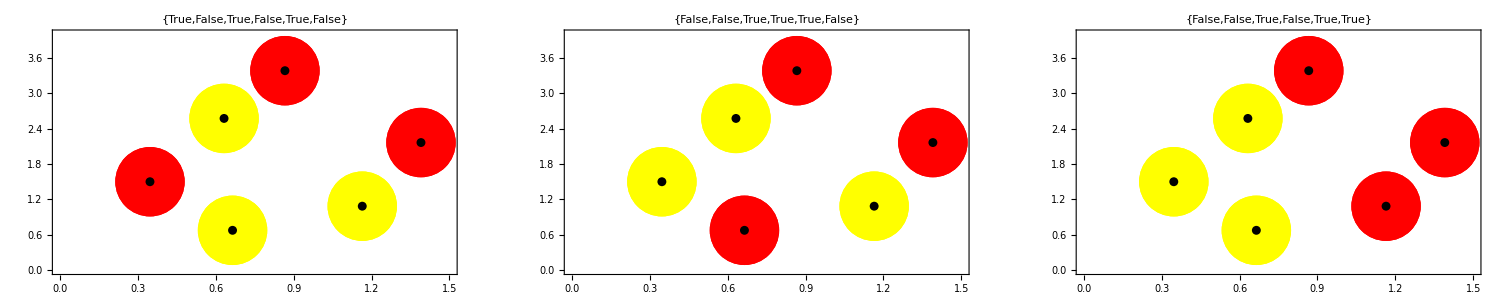

```mathematica
i1={1,3,5};
i2={3,4,5};
i3={3,5,6};
GraphicsRow[{plot[i1],plot[i2],plot[i3]},ImageSize->1500]
```

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms\\Graphics"]
Export["101010.jpg",plot[i1]]
Export["001110.jpg",plot[i2]]
Export["001011.jpg",plot[i3]]
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms\Graphics

101010.jpg

001110.jpg

001011.jpg

```mathematica
SetDirectory["C:\\Users\\Saesun Kim\\Documents\\Team10\\Week2_Rydberg_Atoms"]
data=Import["task2_data.dat","List"];
```

C:\Users\Saesun Kim\Documents\Team10\Week2_Rydberg_Atoms

110100 â.82.8dâ.82.82â.82.8e

```mathematica
dataList=Table[StringTake[data[[i]],6],{i,1,Length[data]}];
```

{{110100,2877},{010101,2845},{011100,2808},{011101,276},{001100,79},{100100,69},{000101,86},{110001,7},{011000,73},{010100,60},{110101,297},{111100,283},{010001,87},{110000,86},{100110,1},{001010,10},{111000,8},{101100,6},{001101,3},{011001,6},{100101,7},{000100,2},{000011,10},{100010,6},{000111,1},{010000,1},{101010,1},{001011,2},{000001,1},{001000,1},{100000,1}}

```mathematica
Block[{t=SortBy[Tally[dataList],Last]},TableForm[t,TableHeadings->{None,{"Number","Frequency"}}]]
```

Number | Frequency
000001 | 1
000111 | 1
001000 | 1
010000 | 1
100000 | 1
100110 | 1
101010 | 1
000100 | 2
001011 | 2
001101 | 3
011001 | 6
100010 | 6
101100 | 6
100101 | 7
110001 | 7
111000 | 8
000011 | 10
001010 | 10
010100 | 60
100100 | 69
011000 | 73
001100 | 79
000101 | 86
110000 | 86
010001 | 87
011101 | 276
111100 | 283
110101 | 297
011100 | 2808
010101 | 2845
110100 | 2877